```mathematica
NS[]
```

```mathematica
rg=Range[0,2];
```

```mathematica
nd[distr_]:=Append[distr,1-Total@distr]
```

```mathematica
extrpoints={Cos[#],Sin[#]}&/@{Pi/2,Pi/2-2*Pi/3,Pi/2-4*Pi/3};
affmap=T@extrpoints
```

{{0,(√3)/2,-(√3)/2},{1,-1/2,-1/2}}

```mathematica
revmap[x_,y_]=PseudoInverse[affmap].{x,y}+{1,1,1}/3
```

{1/3+(2 y)/3,1/3+x/(√3)-y/3,1/3-x/(√3)-y/3}

```mathematica
simplex=Line[Append[#,#[[1]]]&@extrpoints];
outsimplex={White,Opacity[0],Line[Append[#,#[[1]]]&@(extrpoints*1.1)]};
```

```mathematica
quantum=6;reprlist=(Flatten[Permutations/@IntegerPartitions[quantum+3,{3}],1]-1)/quantum;
```

```mathematica
chart[ndistr_]:=BarChart[{ndistr},PlotRange->{0,1},Axes->True,Frame->False,Ticks->None,ChartStyle->Directive[{grey,Opacity[1],EdgeForm[None]}],
AxesStyle->Directive[{Black,Thickness[0.04]}],BarSpacing->{Automatic,1}
(*"FixedBarSpacing"->True*)]
```

```mathematica
sz=0.15;Show[base=Graphics[Join[{outsimplex,simplex},Inset[chart[#],
affmap.#,{Center,-0.1},sz]&/@reprlist,{green,Point[affmap.#]}&/@reprlist]],Padding->100]
```

```mathematica
expng["hyp_space_pic",base]
```

hyp_space_pic.png

```mathematica
meanspikes=0.2;weight=10;
basedistr=(#/Total[#])&@(PDF[GeometricDistribution[1/(meanspikes+1)],#]&/@rg);
superdistr[ndistr_]:=PDF[DirichletDistribution[weight*basedistr],ndistr[[;;-2]]]
```

```mathematica
pdf=Plot3D[superdistr[revmap[x,y]]/100,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},And@@Flatten[(0<=#≤1)&/@revmap[x,y]]],
PlotRange->{0,All},ViewPoint->Dynamic[viewpoint],BoxRatios->{2,2,1},Mesh->None,Axes->True,PlotStyle->Directive[{Opacity[0.5],blue}]]
```

```mathematica
0.008,0.4
```

```mathematica
texture={Texture[base],Polygon[Append[#,-0.001/10]&/@(extrpoints*1.1),VertexTextureCoordinates->{{1/2,1},{1,0},{0,0}}]};
```

```mathematica
finaldistr=Show[{Graphics3D[texture,Lighting->"Neutral",BoxRatios->{2,2,1}],pdf},ViewPoint->Dynamic[viewpoint]]
```

```mathematica
expng["distr_w10_pict",finaldistr]
```

distr_w10_pict.png

```mathematica
mycolorfunction[z_,sup_:1]=Opacity[0.75,If[z/sup≥0,Blend[{White,red},z/sup],Blend[{White,blue},-z/sup]]];
```

```mathematica
meanspikes=0.2;weight=10;
basedistr=Append[#[[;;2]],1-Total[#[[;;2]]]]&@((#/Total@#)&@(PDF[GeometricDistribution[1/(meanspikes+1)],#]&/@Range[0,15]));
superdistr[ndistr_]:=PDF[DirichletDistribution[weight*basedistr],ndistr[[;;-2]]]
```

```mathematica
dpdf=DensityPlot[superdistr[revmap[x,y]],{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},And@@Flatten[(0<=#≤1)&/@revmap[x,y]]],
PlotRange->All,Mesh->None,Axes->False,Frame->False,ColorFunction->mycolorfunction,ColorFunctionScaling->True,PlotPoints->50]
```

```mathematica
heatd=Show[{base,dpdf}]
```

```mathematica
expng["heatdistr_w01_pict",heatd]
```

heatdistr_w01_pict.png

```mathematica
mycolorfunction[z_,sup_:1]=Opacity[0.75,If[z/sup≥0,Blend[{White,red},z/sup],Blend[{White,blue},-z/sup]]];
```

```mathematica
meanspikes=0.2;weight=10;
basedistr=Append[#[[;;2]],1-Total[#[[;;2]]]]&@((#/Total@#)&@(PDF[GeometricDistribution[1/(meanspikes+1)],#]&/@Range[0,15]));
superdistr[ndistr_]:=PDF[DirichletDistribution[weight*basedistr],ndistr[[;;-2]]]
```

```mathematica
nsamples=1024;samples=Append[#,1-Total@#]&/@RandomVariate[DirichletDistribution[weight*basedistr],nsamples];
```

```mathematica
dpdf=ListPlot[Evaluate[samples.T[affmap]],Joined->False,
PlotRange->All,Axes->False,Frame->False,PlotStyle->Directive[{Opacity[0.5],red}]];
```

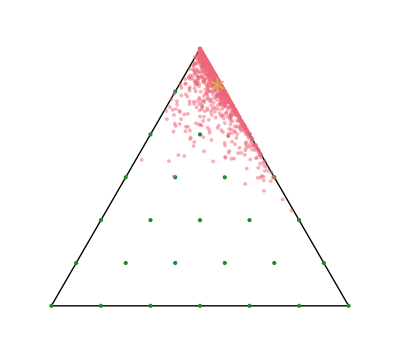
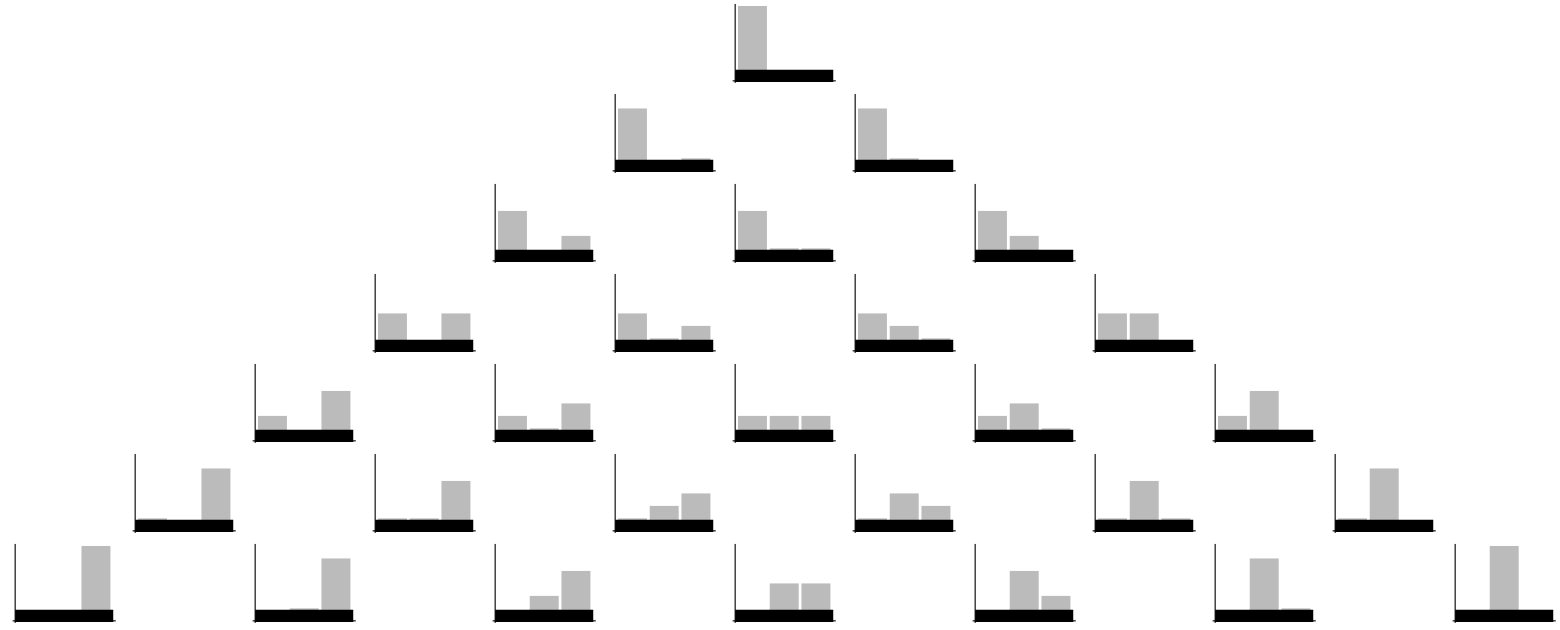

```mathematica
heatd=Show[{base,dpdf,Graphics[{yellow,Inset[Style["*",30],affmap.basedistr,Center]}]}]
```

```mathematica
expng["scatterdistr_w10_pict",heatd]
```

scatterdistr_w10_pict.png

```mathematica
affmap
```

{{0,(√3)/2,-(√3)/2},{1,-1/2,-1/2}}